# 5 - Answers to challenges

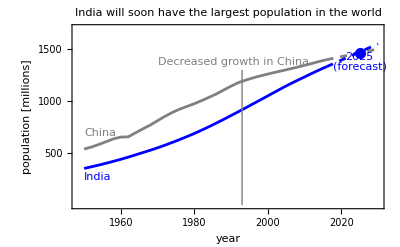

```mathematica
(* Challenge 1 *)

genLines[lines_, startPt_, spacing_, offset_, opts:OptionsPattern[Style]] := 	
	Table[Style[Text[lines⟦n+1⟧, startPt - n{0,spacing}, offset],
		  opts], {n, 0, Length[lines]-1}]
		  
popChina = Table[{year, CountryData["China", {{"Population"}, year}]/1000000},
				  {year, 1950, 2017, 2}];
popIndia = Table[{year, CountryData["India", {{"Population"}, year}]/1000000},
				  {year, 1950, 2017, 2}];
forecastChina = {Last@popChina//QuantityMagnitude, {2030, 1500}};
forecastIndia = {Last@popIndia//QuantityMagnitude, {2030, 1550}};

ListPlot[{popChina, popIndia, forecastChina, forecastIndia},
	Joined->True,
	Frame->{True,True,False,False},
	FrameLabel->{"year", "population [millions]"},
	PlotLabel->"India will soon have the largest population in the world",
	PlotStyle->{
		Gray,
		Blue,
		Directive[Gray,Dashed],
		Directive[Blue,Dashed]
	},
	PlotRange->{Automatic,{0,1700}},
	FrameTicks->{{1960,1980,2000,2020},
				{500,1000,1500}},
	
	Epilog->{
		PointSize[0.02],
		Blue,
		Point[{2025, 1460}],
		Text["2025", {2025,1420}, {0,1}],
		Text["(forecast)", {2025,1330}, {0,1}],
		Gray,		
		Text["China", {1950,650}, {-1,-1}],
		Blue,
		Text["India", {1950,220}, {-1,-1}],
		Gray,
		Line[{{1993,0}, {1993,1300}}],
		Text["Decreased growth in China",
			 {1970,1330}, {-1,-1}]
	}
]
```

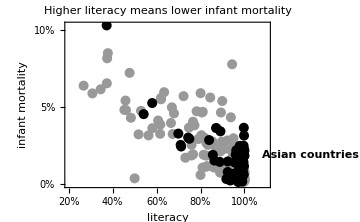

```mathematica
(* Challenge 2 *)

countries = CountryData["Countries"];
infMort = Map[CountryData[#, "InfantMortalityFraction"]&, countries];
literacy = Map[CountryData[#, "LiteracyFraction"]&, countries];
pts = Transpose[{literacy, infMort}];

saCountries = Select[countries, SameQ[CountryData[#, "Continent"],
                                      CountryData["China", "Continent"]]&];
sainfMort = Map[CountryData[#, "InfantMortalityFraction"]&, saCountries];
saliteracy = Map[CountryData[#, "LiteracyFraction"]&, saCountries];
saPts = Transpose[{saliteracy, sainfMort}];
nonsaCountries = Complement[countries,saCountries];
nonsainfMort = Map[CountryData[#, "InfantMortalityFraction"]&, nonsaCountries];
nonsaliteracy = Map[CountryData[#, "LiteracyFraction"]&, nonsaCountries];
nonsaPts = Transpose[{nonsaliteracy, nonsainfMort}];
hlColour = Black;

ListPlot[{nonsaPts, saPts},
	Frame->{True,True,False,False},
	PlotStyle->{Directive[PointSize[0.02], GrayLevel[0.6]],
	           Directive[PointSize[0.02], hlColour]},
	PlotLabels->{None, Placed[Style["Asian countries", hlColour, Bold], After]},
	FrameLabel->{"literacy", "infant mortality"},
	PlotRange->{{0.2,1.1},Automatic},
	PlotLabel->"Higher literacy means lower infant mortality",
	FrameTicks->{{{.2,"20%"}, {.4,"40%"}, {.6,"60%"}, {.8,"80%"}, {1,"100%"}},
		        {{0,"0%"},{0.05,"5%"}, {0.1,"10%"}, {0.15,"15%"}}},
	ImageSize->Medium
]
```